Gaussian

```mathematica
$Assumptions={τ>0,τR>0,t>=0,τ-t>=0};
```

```mathematica
Psi[t_]=Exp[-π/4(t/τR)^2];
dPsi[t_]=D[Psi[t],t];
ddPsi[t_]=D[dPsi[t],t];
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi[t],t,s]);

c0=SeriesCoefficient[f[s],{s,0,0}];
```

```mathematica
g[t_]=(t+τR)/(τ+2τR);

gs[t_]=c0(DiracDelta[t]-DiracDelta[τ-t])/(τ+2τR);


h1[t_]=t/τ;
h2[t_]=t/τ+Sin[ π t/τ];
```

```mathematica
Wh1[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]h1[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]h1[t]h1[u],{t,0,τ},{u,0,τ}];
```

```mathematica
Wh2[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]h2[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]h2[t]h2[u],{t,0,τ},{u,0,τ}]
```

-1/2+(τR Erf[(√π τ)/(2 τR)])/τ-(ⅈ ⅇ^(-(π τR^2)/τ^2) π τR (Erfi[√π (-(ⅈ τ)/(2 τR)+τR/τ)]-Erfi[√π ((ⅈ τ)/(2 τR)+τR/τ)]))/(2 τ)-1/(16 τ^3)(-8 τ^3+(32 τ τR^2)/π-(32 ⅇ^(-(π τ^2)/(4 τR^2)) τ τR^2)/π+16 π τ τR^2+16 ⅇ^(-(π τ^2)/(4 τR^2)) π τ τR^2+ⅈ ⅇ^(-(π τR^2)/τ^2) τR ((4-(1-8 ⅈ) π+4 ⅈ π^2) τ^2+8 π^2 τR^2) Erf[(√π (τ^2-2 ⅈ τR^2))/(2 τ τR)]-4 ⅇ^(-(π τR^2)/τ^2) π τR (((2-ⅈ)+π) τ^2+2 ⅈ π τR^2) Erf[(√π (τ^2+2 ⅈ τR^2))/(2 τ τR)]+8 ⅇ^(-(π τR^2)/τ^2) π τ^2 τR Erfi[(√π τR)/τ]-16 ⅇ^(-(π τR^2)/τ^2) π^2 τR^3 Erfi[(√π τR)/τ]-4 ⅇ^(-(π τR^2)/τ^2) τ^2 τR Erfi[√π ((ⅈ τ)/(2 τR)+τR/τ)]-3 ⅇ^(-(π τR^2)/τ^2) π τ^2 τR Erfi[√π ((ⅈ τ)/(2 τR)+τR/τ)])

```mathematica
W0[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]g[t]g[u],{t,0,τ},{u,0,τ}]
```

1/2-(4 τR^2-π (τ^2+2 τ τR+2 τR^2)+2 ⅇ^(-(π τ^2)/(4 τR^2)) τR (-2 τR+π (τ+τR)))/(2 π (τ+2 τR)^2)-(τ-ⅇ^(-(π τ^2)/(4 τR^2)) τR+τR Erfc[(√π τ)/(2 τR)])/(τ+2 τR)

```mathematica
W1[τ_]=W0[τ]+c0 dPsi[τ]/(τ+2τR)-c0/(τ+2τR)Integrate[ddPsi[t]g[t],{t,0,τ}]+c0/(τ+2τR)Integrate[ddPsi[τ-t]g[t],{t,0,τ}]-c0^2/(τ+2τR)^2 ddPsi[0]+c0^2/(τ+2τR)^2 ddPsi[τ]
```

1/2+((-2+π)^2 τR^2)/(2 π (τ+2 τR)^2)+((-2+π)^2 ((ⅇ^(-(π τ^2)/(4 τR^2)) π^2 τ^2)/(4 τR^4)-(ⅇ^(-(π τ^2)/(4 τR^2)) π)/(2 τR^2)) τR^4)/(π^2 (τ+2 τR)^2)-(ⅇ^(-(π τ^2)/(4 τR^2)) (-2+π) τ)/(2 (τ+2 τR))+((-2+π) τR (-2 τR+ⅇ^(-(π τ^2)/(4 τR^2)) (-π τ+2 τR)))/(2 π (τ+2 τR)^2)-(4 τR^2-π (τ^2+2 τ τR+2 τR^2)+2 ⅇ^(-(π τ^2)/(4 τR^2)) τR (-2 τR+π (τ+τR)))/(2 π (τ+2 τR)^2)-((-2+π) (2 τR^2+ⅇ^(-(π τ^2)/(4 τR^2)) (-2 τR^2-π τ (τ+τR))))/(2 π (τ+2 τR)^2)-(τ-ⅇ^(-(π τ^2)/(4 τR^2)) τR+τR Erfc[(√π τ)/(2 τR)])/(τ+2 τR)

```mathematica
Wh1[τ_]=-1/2+1/2 (1-(4 (1-ⅇ^(-(π τ^2)/(4 τR^2))) τR^2)/(π τ^2))+(τR Erf[(√π τ)/(2 τR)])/τ;
```

```mathematica
Wh2[τ_]=-1/2+(τR Erf[(√π τ)/(2 τR)])/τ-(ⅈ ⅇ^(-(π τR^2)/τ^2) π τR (Erfi[√π (-(ⅈ τ)/(2 τR)+τR/τ)]-Erfi[√π ((ⅈ τ)/(2 τR)+τR/τ)]))/(2 τ)-1/(16 τ^3)(-8 τ^3+(32 τ τR^2)/π-(32 ⅇ^(-(π τ^2)/(4 τR^2)) τ τR^2)/π+16 π τ τR^2+16 ⅇ^(-(π τ^2)/(4 τR^2)) π τ τR^2+ⅈ ⅇ^(-(π τR^2)/τ^2) τR ((4-(1-8 ⅈ) π+4 ⅈ π^2) τ^2+8 π^2 τR^2) Erf[(√π (τ^2-2 ⅈ τR^2))/(2 τ τR)]-4 ⅇ^(-(π τR^2)/τ^2) π τR (((2-ⅈ)+π) τ^2+2 ⅈ π τR^2) Erf[(√π (τ^2+2 ⅈ τR^2))/(2 τ τR)]+8 ⅇ^(-(π τR^2)/τ^2) π τ^2 τR Erfi[(√π τR)/τ]-16 ⅇ^(-(π τR^2)/τ^2) π^2 τR^3 Erfi[(√π τR)/τ]-4 ⅇ^(-(π τR^2)/τ^2) τ^2 τR Erfi[√π ((ⅈ τ)/(2 τR)+τR/τ)]-3 ⅇ^(-(π τR^2)/τ^2) π τ^2 τR Erfi[√π ((ⅈ τ)/(2 τR)+τR/τ)]);
```

```mathematica
W0[τ_]=1/2-(4 τR^2-π (τ^2+2 τ τR+2 τR^2)+2 ⅇ^(-(π τ^2)/(4 τR^2)) τR (-2 τR+π (τ+τR)))/(2 π (τ+2 τR)^2)-(τ-ⅇ^(-(π τ^2)/(4 τR^2)) τR+τR Erfc[(√π τ)/(2 τR)])/(τ+2 τR);
```

```mathematica
W1[τ_]=1/2+((-2+π)^2 τR^2)/(2 π (τ+2 τR)^2)+((-2+π)^2 ((ⅇ^(-(π τ^2)/(4 τR^2)) π^2 τ^2)/(4 τR^4)-(ⅇ^(-(π τ^2)/(4 τR^2)) π)/(2 τR^2)) τR^4)/(π^2 (τ+2 τR)^2)-(ⅇ^(-(π τ^2)/(4 τR^2)) (-2+π) τ)/(2 (τ+2 τR))+((-2+π) τR (-2 τR+ⅇ^(-(π τ^2)/(4 τR^2)) (-π τ+2 τR)))/(2 π (τ+2 τR)^2)-(4 τR^2-π (τ^2+2 τ τR+2 τR^2)+2 ⅇ^(-(π τ^2)/(4 τR^2)) τR (-2 τR+π (τ+τR)))/(2 π (τ+2 τR)^2)-((-2+π) (2 τR^2+ⅇ^(-(π τ^2)/(4 τR^2)) (-2 τR^2-π τ (τ+τR))))/(2 π (τ+2 τR)^2)-(τ-ⅇ^(-(π τ^2)/(4 τR^2)) τR+τR Erfc[(√π τ)/(2 τR)])/(τ+2 τR);
```

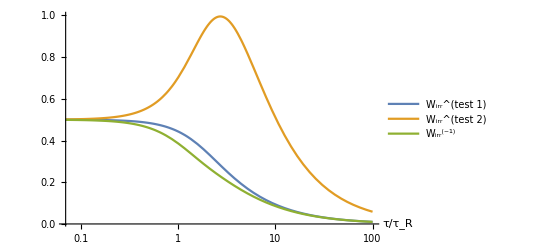

```mathematica
τR=1;
LogLinearPlot[{Legended[Wh1[τ],"W_irr^(test 1)"],Legended[Wh2[τ],"W_irr^(test 2)"],Legended[W0[τ],"W_irr^(-1)"]},{τ,0.07,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR]
```

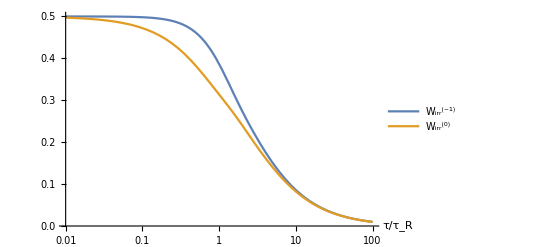

```mathematica
τR=1;
LogLinearPlot[{Legended[W0[τ],"W_irr^(-1)"],Legended[W1[τ],"W_irr^(0)"]},{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR]
```

```mathematica
ϵ1[τ_]= Abs[(W1[τ]-W0[τ])/W1[τ]];
```

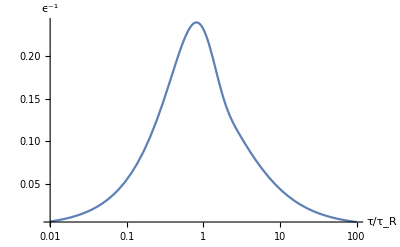

```mathematica
τR=1;
LogLinearPlot[ϵ1[τ],{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R","ϵ^-1"}]
Clear[τR]
```

```mathematica
τR=1;

data=Table[{τ,ϵ1[τ]},{τ,0.001,0.01,0.001/100}];

Do[

aux=Table[{τ,ϵ1[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data=AppendTo[data,aux[[j]]];

,{j,1,91}];

,{n,1,4}];

Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi4.dat",data];

Clear[τR]
```